# CrSBr double layer magnon dispersion with applied magnetic field

To calculate the dipolar magnon dispersion, we express the magnetization of each sublattice as the summation of the equilibrium magnetization and dynamic magnetization. 
That is,

We aim to solve the Landau-Lifshitz equation 



for the magnon dispersion.

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAll[gamma,Ms,J,Kx,Kz,Hz,Theta,hx,hy,hz,kx,ky,kz];
```

```mathematica
Clear[gamma,Ms,J,Kx,Kz,Hz,Theta,hx,hy,hz,kx,ky,kz];
M1={Ms*Cos[Theta]-ma*Sin[Theta],m1y,Ms*Sin[Theta]+ma*Cos[Theta]};
m1x = M1[[1]];
m1z = M1[[3]];
M2={-Ms*Cos[Theta]-mb*Sin[Theta],m2y,Ms*Sin[Theta]-mb*Cos[Theta]};
m2x = M2[[1]];
m2z = M2[[3]];
```

For the first sublattice, the equilibrium magnetization is along the direction (cos(θ), 0, sin(θ)), so the two axes for the dynamic magnetization are (-sin(θ), 0, cos(θ)) (m_a direction) and (0, 1, 0) (m_(1y) direction). For the second sublattice, the equilibrium magnetization is along the direction (-cos(θ), 0, sin(θ)), so the two axes for the dynamic magnetization are (-sin(θ), 0, -cos(θ)) (m_b direction) and (0, 1, 0) (m_(2y) direction). The effective field H_i^eff is calculated below.

```mathematica
H1 = {(2*Kx*m1x)/Ms^2-(J*m2x)/Ms^2+hx,(-J*m2y)/Ms^2+hy,(-2*Kz*m1z)/Ms^2-(J*m2z)/Ms^2+Hz+hz};
H2 = {(2*Kx*m2x)/Ms^2-(J*m1x)/Ms^2+hx,(-J*m1y)/Ms^2+hy,(-2*Kz*m2z)/Ms^2-(J*m1z)/Ms^2+Hz+hz};
```

Then we calculate the cross-product term ). We start with the cross product term along the m_(1y) direction for the first sublattice.

```mathematica
CrossM1=FullSimplify[Cross[M1,H1]];
CrossM1[[2]]
```

(hx ma-(hz+Hz) Ms) Cos[Theta]+(((J+2 (Kx+Kz)) ma-J mb) Cos[2 Theta])/Ms+(hz+Hz) ma Sin[Theta]+hx Ms Sin[Theta]+(J+Kx+Kz) Sin[2 Theta]+(ma (-((Kx+Kz) ma)+J mb) Sin[2 Theta])/Ms^2

We ignore second order terms in  and  (since they are assumed to be small?)

```mathematica
Cross1y=(Series[CrossM1[[2]]/.{ma->t*ma,mb->t*mb,hx->t*hx,hy->t*hy,hz->t*hz,m1y->t*m1y,m2y->t*m2y},{t,0,1}]//Normal)/.{t->1}
```

-hz Ms Cos[Theta]-Hz Ms Cos[Theta]+(((J+2 (Kx+Kz)) ma-J mb) Cos[2 Theta])/Ms+Hz ma Sin[Theta]+hx Ms Sin[Theta]+(J+Kx+Kz) Sin[2 Theta]

Then we also get the cross product along the  direction for sublattice 1 via

```mathematica
Cross1a = FullSimplify[CrossM1.{-Sin[Theta],0,Cos[Theta]}]
```

(Ms (-Kx m1y+Kz m1y-J m2y+hy Ms^2)+m1y (-hx Ms^2 Cos[Theta]-(J+Kx+Kz) Ms Cos[2 Theta]-(hz+Hz) Ms^2 Sin[Theta]+((Kx+Kz) ma-J mb) Sin[2 Theta]))/Ms^2

And again we only keep first order terms in the m and h

```mathematica
Cross1a = (Series[Cross1a/.{ma->t*ma,mb->t*mb,hx->t*hx,hy->t*hy,hz->t*hz,m1y->t*m1y,m2y->t*m2y},{t,0,1}]//Normal)/.{t->1}
```

(Ms (-Kx m1y+Kz m1y-J m2y+hy Ms^2)+m1y (-((J+Kx+Kz) Ms Cos[2 Theta])-Hz Ms^2 Sin[Theta]))/Ms^2

Now we repeat for the second sublattice, only calculating the cross product along the  direction

```mathematica
CrossM2=FullSimplify[Cross[M2,H2]];
CrossM2[[2]]
```

(-hx mb+(hz+Hz) Ms) Cos[Theta]+((-J ma+(J+2 (Kx+Kz)) mb) Cos[2 Theta])/Ms+((hz+Hz) mb+hx Ms) Sin[Theta]-(J+Kx+Kz) Sin[2 Theta]+(mb (-J ma+(Kx+Kz) mb) Sin[2 Theta])/Ms^2

```mathematica
Cross2y = (Series[CrossM2[[2]]/.{ma->t*ma,mb->t*mb,hx->t*hx,hy->t*hy,hz->t*hz},{t,0,1}]//Normal)/.{t->1}

Cross2b = FullSimplify[CrossM2.{-Sin[Theta],0,-Cos[Theta]}]
```

hz Ms Cos[Theta]+Hz Ms Cos[Theta]+((-J ma+(J+2 (Kx+Kz)) mb) Cos[2 Theta])/Ms+(Hz mb+hx Ms) Sin[Theta]-(J+Kx+Kz) Sin[2 Theta]

(Ms (-J m1y-Kx m2y+Kz m2y+hy Ms^2)+m2y (hx Ms^2 Cos[Theta]-(J+Kx+Kz) Ms Cos[2 Theta]-(hz+Hz) Ms^2 Sin[Theta]+(J ma-(Kx+Kz) mb) Sin[2 Theta]))/Ms^2

```mathematica
Cross2b = (Series[Cross2b/.{ma->t*ma,mb->t*mb,hx->t*hx,hy->t*hy,hz->t*hz,m1y->t*m1y,m2y->t*m2y},{t,0,1}]//Normal)/.{t->1}
```

(Ms (-J m1y-Kx m2y+Kz m2y+hy Ms^2)+m2y (-((J+Kx+Kz) Ms Cos[2 Theta])-Hz Ms^2 Sin[Theta]))/Ms^2

Now for the angle , which determines the direction of equilibrium magnetization, there are two cases:

      if       
                               if      

where  is the saturation magnetic field 
Case 1 is below

```mathematica
Hs = 2(J+Kx+Kz)/Ms;
If[Hz>Hs, Print[Text[Warning! Hz > Hs so case one does not apply]]];
```

```mathematica
Theta =ArcSin[Hz/Hs]
```

ArcSin[(Hz Ms)/(2 (J+Kx+Kz))]

```mathematica
Cross1a1=FullSimplify[Cross1a]
Cross1y1 =FullSimplify[ Cross1y]
Cross2b1 = FullSimplify[Cross2b]
Cross2y1=FullSimplify[Cross2y]
```

(-2 Kx m1y-J (m1y+m2y)+hy Ms^2)/Ms

(Hz Ms (Hz ma+hx Ms))/(2 (J+Kx+Kz))+((2 (Kx+Kz) ma+J (ma-mb)) (2 (J+Kx+Kz)^2-Hz^2 Ms^2))/(2 (J+Kx+Kz)^2 Ms)-hz Ms √(1-(Hz^2 Ms^2)/(4 (J+Kx+Kz)^2))

(-2 Kx m2y-J (m1y+m2y)+hy Ms^2)/Ms

(Hz Ms (Hz mb+hx Ms))/(2 (J+Kx+Kz))+((2 (Kx+Kz) mb+J (-ma+mb)) (2 (J+Kx+Kz)^2-Hz^2 Ms^2))/(2 (J+Kx+Kz)^2 Ms)+hz Ms √(1-(Hz^2 Ms^2)/(4 (J+Kx+Kz)^2))

Note that cos(2arcsin(x)) = 1-2x^2. So we can simplify Cross1y and Cross2y

```mathematica
TrigExpand[Cos[2ArcSin[x]]]
```

1-2 x^2

```mathematica
Cross1y1 = FullSimplify[TrigExpand[Cross1y1]]
Cross2y1 = FullSimplify[TrigExpand[Cross2y1]]
```

1/2 ((4 Kx ma)/Ms+(2 J ma+4 Kz ma-2 J mb)/Ms+(Hz^2 J (ma+mb) Ms)/(J+Kx+Kz)^2+(Hz Ms (-Hz ma+hx Ms))/(J+Kx+Kz)-hz Ms √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2))

1/2 ((4 (Kx+Kz) mb)/Ms+(2 J (-ma+mb))/Ms-(Hz^2 (Kx+Kz) (ma+mb) Ms)/(J+Kx+Kz)^2+(Hz Ms (Hz ma+hx Ms))/(J+Kx+Kz)+hz Ms √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2))

```mathematica
(*Manual version: Cross1y = FullSimplify[1/2 Ms ((Hz (Hz ma+hx Ms))/(J+Kx+Kz)-hz √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2))+((2 (Kx+Kz) ma+J (ma-mb)) (1-2 ((Hz Ms)/(2 (J+Kx+Kz)))^2))/Ms]
Cross2y = FullSimplify[1/2 Ms ((Hz (Hz mb+hx Ms))/(J+Kx+Kz)+hz √(4-(Hz^2 Ms^2)/(J+Kx+Kz)^2))+((2 (Kx+Kz) mb+J (-ma+mb))(1-2 ((Hz Ms)/(2 (J+Kx+Kz)))^2))/Ms] *)
```

Now solving the LL equation and assuming the m’s and h’s have the form of plane waves, we can express 
in terms of

```mathematica
Clear[omega];
sol1=FullSimplify[Solve[I*omega*m1y==gamma*Cross1y1 && I*omega*ma==gamma*Cross1a1 && I*omega*m2y==gamma*Cross2y1 && I*omega*mb==gamma*Cross2b1 ,{m1y,ma,m2y,mb}]];
M1y=FullSimplify[(m1y/.sol1)][[1]];
Ma=FullSimplify[(ma/.sol1)][[1]];
M2y=FullSimplify[(m2y/.sol1)][[1]];
Mb=FullSimplify[(mb/.sol1)][[1]];
```

We change coordinates for net dynamic magnetization to xyz from aby

```mathematica
Mx = FullSimplify[-Ma*Sin[Theta]-Mb*Sin[Theta]]
My = FullSimplify[M1y+M2y]
Mz = FullSimplify[Ma*Cos[Theta]-Mb*Cos[Theta]]
```

(gamma Hz Ms^4 (gamma hx Hz (J+Kx)-ⅈ hy (J+Kx+Kz) omega))/(gamma^2 (J+Kx) (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2)-(J+Kx+Kz)^2 Ms^2 omega^2)

(gamma Ms^2 (gamma hy (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2)+ⅈ hx Hz (J+Kx+Kz) Ms^2 omega))/(gamma^2 (J+Kx) (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2)-(J+Kx+Kz)^2 Ms^2 omega^2)

(gamma^2 hz Kx Ms^2 (4 (J+Kx+Kz)^2-Hz^2 Ms^2))/((J+Kx+Kz) (gamma^2 Kx (4 (J+Kx+Kz)^2-Hz^2 Ms^2)-(J+Kx+Kz) Ms^2 omega^2))

Next we calculate  and use the Maxwell equation  to solve for the magnon dispersion

```mathematica
{bx, by, bz} = {hx + 4Pi*Mx, hy + 4 Pi*My, hz + 4 Pi*Mz}
```

{hx+(4 gamma Hz Ms^4 (gamma hx Hz (J+Kx)-ⅈ hy (J+Kx+Kz) omega) π)/(gamma^2 (J+Kx) (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2)-(J+Kx+Kz)^2 Ms^2 omega^2),hy+(4 gamma Ms^2 (gamma hy (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2)+ⅈ hx Hz (J+Kx+Kz) Ms^2 omega) π)/(gamma^2 (J+Kx) (4 (Kx+Kz) (J+Kx+Kz)^2-Hz^2 (-J+Kx+Kz) Ms^2)-(J+Kx+Kz)^2 Ms^2 omega^2),hz+(4 gamma^2 hz Kx Ms^2 (4 (J+Kx+Kz)^2-Hz^2 Ms^2) π)/((J+Kx+Kz) (gamma^2 Kx (4 (J+Kx+Kz)^2-Hz^2 Ms^2)-(J+Kx+Kz) Ms^2 omega^2))}

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms,Hz];
dispersion1=Solve[Coefficient[bx,hx]*kx^2+Coefficient[by,hy]*ky^2+Coefficient[bz,hz]*kz^2==0,{omega}];
omegaSol1 = omega/.dispersion1;
omega1 = omegaSol1[[1]]/(2Pi*10^9);
omega2 = omegaSol1[[2]]/(2Pi*10^9);
omega3 = omegaSol1[[3]]/(2Pi*10^9);
omega4=omegaSol1[[4]]/(2Pi*10^9);
```

```mathematica
omega2CV=omega2/.{kx->kz*px,ky->kz*py};
```

```mathematica
omega4CV=omega4/.{kx->kz*px,ky->kz*py};
```

## Case 2: H_z > 2(J + K_x + K_z)/M_s

Following the same process as case one, except here we use Theta = Pi/2

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms,Hz]
```

```mathematica
Theta = Pi/2;
```

```mathematica
Cross1a2=FullSimplify[Cross1a]
Cross1y2 =FullSimplify[ Cross1y]
Cross2b2 = FullSimplify[Cross2b]
Cross2y2=FullSimplify[Cross2y]
```

-Hz m1y+(J m1y+2 Kz m1y-J m2y)/Ms+hy Ms

Hz ma+(-((J+2 (Kx+Kz)) ma)+J mb)/Ms+hx Ms

-Hz m2y+(2 Kz m2y+J (-m1y+m2y))/Ms+hy Ms

Hz mb+(J ma-(J+2 (Kx+Kz)) mb)/Ms+hx Ms

```mathematica
(*Cross1y2 = FullSimplify[TrigExpand[Cross1y2]]
Cross2y2 = FullSimplify[TrigExpand[Cross2y2]]*)
```

```mathematica
Clear[omega];
sol2=FullSimplify[Solve[I*omega*m1y==gamma*Cross1y2 && I*omega*ma==gamma*Cross1a2 && I*omega*m2y==gamma*Cross2y2 && I*omega*mb==gamma*Cross2b2 ,{m1y,ma,m2y,mb}]];
M1y=FullSimplify[(m1y/.sol2)][[1]];
Ma=FullSimplify[(ma/.sol2)][[1]];
M2y=FullSimplify[(m2y/.sol2)][[1]];
Mb=FullSimplify[(mb/.sol2)][[1]];
```

```mathematica
Mx = FullSimplify[-Ma*Sin[Theta]-Mb*Sin[Theta]]
My = FullSimplify[M1y+M2y]
Mz = FullSimplify[Ma*Cos[Theta]-Mb*Cos[Theta]]
```

(2 gamma Ms^2 (gamma hx (-2 Kz+Hz Ms)-ⅈ hy Ms omega))/(gamma^2 (2 Kz-Hz Ms) (2 (Kx+Kz)-Hz Ms)-Ms^2 omega^2)

(2 gamma Ms^2 (gamma hy (-2 (Kx+Kz)+Hz Ms)+ⅈ hx Ms omega))/(gamma^2 (2 Kz-Hz Ms) (2 (Kx+Kz)-Hz Ms)-Ms^2 omega^2)

0

```mathematica
{bx, by, bz} = {hx + 4Pi*Mx, hy + 4 Pi*My, hz + 4 Pi*Mz};
```

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms,Hz];
dispersion2=Solve[Coefficient[bx,hx]*kx^2+Coefficient[by,hy]*ky^2+Coefficient[bz,hz]*kz^2==0,{omega}];
omegaSol2 = omega/.dispersion2;
omegaHigh2=omegaSol2[[2]]/(2 Pi*10^9)
```

(ⅈ gamma √(4 kx^2 Kx Kz+4 Kx ky^2 Kz+4 Kx kz^2 Kz+4 kx^2 Kz^2+4 ky^2 Kz^2+4 kz^2 Kz^2-2 Hz kx^2 Kx Ms-2 Hz Kx ky^2 Ms-2 Hz Kx kz^2 Ms-4 Hz kx^2 Kz Ms-4 Hz ky^2 Kz Ms-4 Hz kz^2 Kz Ms+Hz^2 kx^2 Ms^2+Hz^2 ky^2 Ms^2+Hz^2 kz^2 Ms^2-16 Kx ky^2 Ms^2 π-16 kx^2 Kz Ms^2 π-16 ky^2 Kz Ms^2 π+8 Hz kx^2 Ms^3 π+8 Hz ky^2 Ms^3 π))/(2000000000 √(-kx^2 Ms^2-ky^2 Ms^2-kz^2 Ms^2) π)

Diagonalize 4x4 matrix to get dispersion relation (to do: why does this work?)

```mathematica
A = -gamma*FullSimplify[Coefficient[Cross1y2,ma]]
B = -gamma*FullSimplify[Coefficient[Cross1y2,mb]]
C1 = -gamma*FullSimplify[Coefficient[Cross1a2,m1y]]
D1 = -gamma*FullSimplify[Coefficient[Cross1a2,m2y]]
```

-(gamma (-J-2 (Kx+Kz)+Hz Ms))/Ms

-(gamma J)/Ms

-(gamma (J+2 Kz-Hz Ms))/Ms

(gamma J)/Ms

```mathematica
dispersion2prime = FullSimplify[Eigenvalues[{{0,0,C1,D1},{0,0,D1,C1},{-A,-B,0,0},{-B,-A,0,0}}]]
omegaLow2=dispersion2prime[[3]]/(2 Pi*10^9)
```

{-(gamma √(2 Kz-Hz Ms) √(2 (Kx+Kz)-Hz Ms))/Ms,(gamma √(2 Kz-Hz Ms) √(2 (Kx+Kz)-Hz Ms))/Ms,-(gamma √(2 (J+Kz)-Hz Ms) √(2 (J+Kx+Kz)-Hz Ms))/Ms,(gamma √(2 (J+Kz)-Hz Ms) √(2 (J+Kx+Kz)-Hz Ms))/Ms}

-(gamma √(2 (J+Kz)-Hz Ms) √(2 (J+Kx+Kz)-Hz Ms))/(2000000000 Ms π)

This is recreating the plot in the SunOrenstein code to ensure we haven’t messed anything up (so far only case 1 of the external magnetic field)

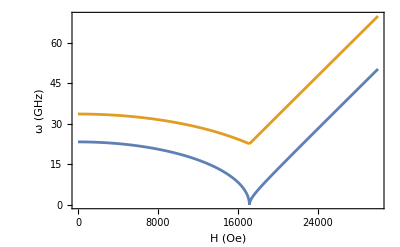

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms];
kx=ky=0;
kz=1;
J = 5.6*10^5;
Kx = 1.9*10^5;
Kz =1.05*10^6;
gamma=2.3*10^7;
Ms=4.2*10^2/2;
Show[Plot[{omegaLow2,omegaHigh2},{Hz,2*(J+Kx+Kz)/Ms,30000}],Plot[{omega2,omega4},{Hz,0,2*(J+Kx+Kz)/Ms}],Frame->True,FrameLabel->{"H (Oe)","ω (GHz)"},PlotRange->All]
```

The following are parameter values for CrSBr used in the SunOrenstein paper
Kx = 2.00×10^4 J/m^3
Kz = 1.10×10^5 J/m^3
J = 6.48×10^4 J/m^3 
Ms = 2.05×10^5 A/m

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms];
a=0.1;
kz=1;
Kx = 2*10^4;
Kz = 1.1*10^5;
J = 6.48*10^4;
gamma=2.3*10^7;
Ms=2.05*10^5;
Hz = 0  (J+Kx+Kz)/Ms;
Plot3D[{omega4},{ky,0.1*-Pi/a,0.1*Pi/a},{kx,0.1*-Pi/a,0.1*Pi/a},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics3D-

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms];
kz=0.1;
Kx = 2*10^4;
Kz = 1.1*10^5;
J = 6.48*10^4;
gamma=2.3*10^7;
Ms=2.05*10^5;
Hz = 0 (J+Kx+Kz)/Ms;
Plot3D[{omega2CV,omega4CV},{px,-1,1},{py,-1,1},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics3D-

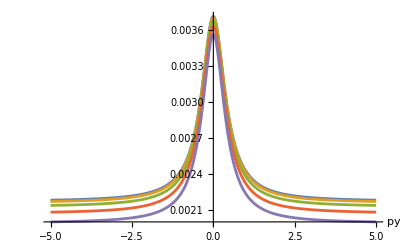

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms];
(* d is sample thickness *)
d=200;
kz=Pi/d;
px=0;
Kx=1.9*10^4;
Kz = 1.1*10^5;
J = 6.48*10^4;
gamma=2.3*10^7;
Ms=2.05*10^5;
T = Table[{omega2CV},{Hz,0*(J+Kx+Kz)/Ms,0.9*(J+Kx+Kz)/Ms,0.2*(J+Kx+Kz)/Ms}];
Plot[T,{py,-5,5},AxesLabel->Automatic,PlotRange->Full]
```

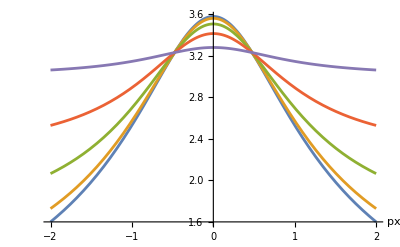

```mathematica
Clear[px,py,kx,ky,kz,J,Kx,Kz,gamma,Ms];
(* d is sample thickness *)
d=200;
kz=Pi/d;
py=0;
Kx=1.9*10^4;
Kz = 1.1*10^5;
J = 6.48*10^4;
gamma=2.3*10^7;
Ms=2.05*10^5;
T = Table[{omega4CV},{Hz,0*(J+Kx+Kz)/Ms,0.8*(J+Kx+Kz)/Ms,0.2*(J+Kx+Kz)/Ms}];
Plot[T,{px,-2,2},AxesLabel->Automatic,PlotRange->Full]
```

```mathematica
kz=0.1;
Kx = 2*10^4;
Kz = 1.1*10^5;
J = 6.48*10^4;
gamma=2.3*10^7;
Ms=2.05*10^5;
Hz = 3 (J+Kx+Kz)/Ms;
Plot3D[{omegaLow2,omegaHigh2},{ky,-1,1},{kx,-1,1},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics3D-

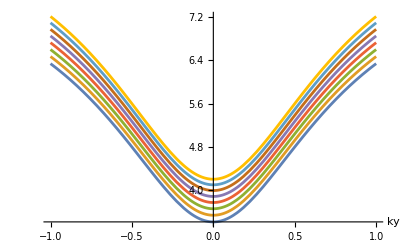

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms];
kz=0.1;
kx=1;
Kz = 1.1*10^5;
J = 6.48*10^4;
gamma=2.3*10^7;
Ms=2.05*10^5;
Hz=(J+Kx+Kz)/Ms;
T = Table[{omega4},{Kx,0.5*10^4,4*10^4,0.5*10^4}];
Plot[T,{ky,-1,1},AxesLabel->Automatic]
```

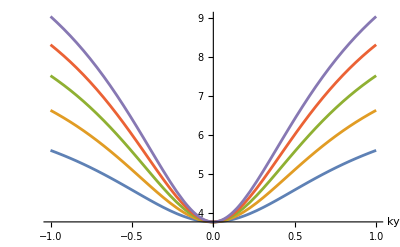

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms];
kz=0.1;
kx=1;
Kx = 2*10^4;
J = 6.48*10^4;
gamma=2.3*10^7;
Ms=2.05*10^5;
Hz=(J+Kx+Kz)/Ms;
T = Table[{omega4},{Kz,0.55*10^5,3*10^5,0.5*10^5}];
Plot[T,{ky,-1,1},AxesLabel->Automatic]
```

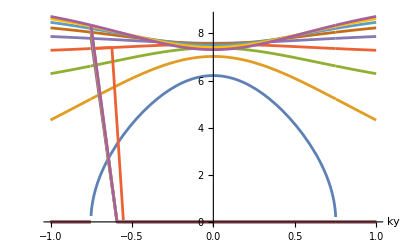

```mathematica
Clear[kx,ky,kz,J,Kx,Kz,gamma,Ms];
kz=0.1;
kx=1;
Kx = 2*10^4;
Kz = 1.1*10^5;
J = 6.48*10^4;
gamma=2.3*10^7;
Ms=2.05*10^5;
Hz=2*(J+Kx+Kz)/Ms;
T = Table[{omega2,omega4},{J,1*10^4,18*10^4,2*10^4}];
Plot[T,{ky,-1,1},AxesLabel->Automatic]
```